```mathematica
ClearAll["GraphPartition`*"]
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

```mathematica
RandomGrid1[m_,n_,maxDist_:1, maxFanOut_:4]:= Module[{elist={},
vlist = Range[1,m*n],
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1],
 newE, neighbor},

Vertex1D[ij_] := (First[ij]-1)*n+Last[ij];
Neighbors[i_,j_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&];
elist={};
Do[AppendTo[elist,{Vertex1D[{i,j}],Vertex1D[neighbor]}],
{i,1,m},{j,1,n},{neighbor, RandomChoice[Neighbors[i,j,maxDist],(*RandomInteger[{1,*)maxFanOut(*}]*)]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ];
(*Make sure that the result graph is connected*)
With[{components=#[[1]]&/@ConnectedComponents[elist]},
If[Length[components]>1,
elist=Join[elist, Map[{components[[1]], #}&,components[[2;;]]]];,
Nothing]];
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->If[Max[m,n]<5,Automatic, None],
System`EdgeStyle->Directive[Opacity[0.5], Thick](*, EdgeShapeFunction->"Arrow"*)];
newG (*UndirectedGraph[newG]*)]
```

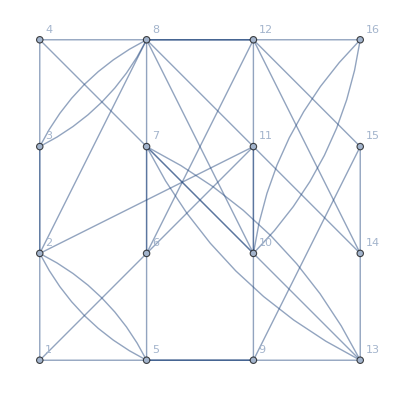
```mathematica
g=-Graphics-;
basisVectors={{0.824942872564313,0.21842747167154472},{0.7726850338214735,0.2627389437815274},{0.38296222200922175,0.8923298892003046},{0.6265355438713063,0.4909949307316633},{1.019269014436307,-0.21252327831065929},{0.31478435493119317,0.8012461230670399},{0.725752689407469,-0.3175338649785955},{0.0479657726172807,1.271845586448928},{0.9414805719375502,-0.2129482325340342},{0.5253186605473394,0.8795991887283106},{0.922373575517376,0.06102973531685047},{0.3535906890163147,0.41577563665363865},{1.655729494964778,-0.9724832046352357},{0.31478435493119317,0.8012461230670402},{0.7713245770034145,-0.8335978818453875},{0.6633076709703752,1.4729574934685317}};
(*{grounds,basisVectors} = FingerprintVectors[g,2, GroundingRandom];
basisVectors = Re[basisVectors];*)
```

{{0.824943,0.218427},{0.772685,0.262739},{0.382962,0.89233},{0.626536,0.490995},{1.01927,-0.212523},{0.314784,0.801246},{0.725753,-0.317534},{0.0479658,1.27185},{0.941481,-0.212948},{0.525319,0.879599},{0.922374,0.0610297},{0.353591,0.415776},{1.65573,-0.972483},{0.314784,0.801246},{0.771325,-0.833598},{0.663308,1.47296}}

#### Melo

```mathematica
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
Norm[Total[basisVectors*meloV]]
N[CriterionPartitionFunction[g,meloV,0.5]]
```

{0,1,1,1,1,1,0,1,0,1,0,1,1,1,0,1}

9.48769

41.8909

#### MeloProbe

```mathematica
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
Norm[Total[basisVectors*meloProbeV]]
N[CriterionPartitionFunction[g,meloProbeV,0.5]]
```

{16,10,13,8,6,14,4,3,2,12,5,1,15,7,11,9}

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1}

2.65912

36.5714

```mathematica
meloProbe2V=VectorMaxOnDirection[basisVectors, V[g]/2, Normalize[Total[basisVectors*meloProbeV]](*+RandomReal[{0,1},3]*)]
Norm[Total[basisVectors*meloProbe2V]]
N[CriterionPartitionFunction[g,meloProbe2V,0.5]]
```

{16,10,8,3,6,14,4,2,12,1,11,13,5,15,7,9}

{0,1,1,1,0,1,0,1,0,1,0,0,0,1,0,1}

7.64707

36.

```mathematica
basisVectors
```

{{0.475185,0.865223},{0.674399,0.14488},{0.807973,0.408165},{0.824622,0.10252},{0.536001,-0.17065},{0.827445,0.11256},{0.361969,-0.546695},{0.915153,0.195494},{0.057361,1.41982},{1.05973,0.133053},{0.441792,0.799402},{0.621307,0.0613409},{0.793446,-1.98442},{0.827445,0.11256},{0.397636,-0.133743},{1.57652,0.214942}}

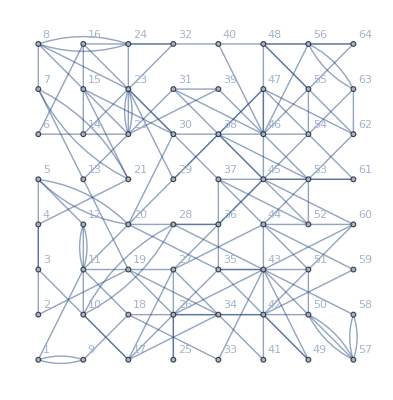
```mathematica
"g"-Graphics-
"basis:"{{0.22597712762192526,0.08676232145143774},{0.38332582419427463,0.11649879529909953},{0.3719834461942282,0.14585185955260452},{0.38737029113979976,0.07325301896506278},{0.3921998285204944,0.08532064441794798},{0.40071445782857906,-0.22260777778021706},{0.36904984605316926,-0.04273193648581907},{0.30037166994058573,-0.07002275192724691},{0.3019343277202663,0.13728990478182368},{0.29802638122989444,0.1574234516789689},{0.36015996748519025,0.13855129403583685},{0.3565958080952721,0.12607311242631125},{0.38772067063200644,-0.007140781660573032},{0.38934576698117546,-0.20591508107479783},{0.4032328410530738,-0.12865486731429573},{0.39624606101566345,-0.22374624002228924},{0.3407595135883375,0.23400493460349317},{0.4380116402566292,0.25389930590594323},{0.36344426958843035,0.17529880609648346},{0.4044980635932933,0.07875534037188303},{0.3861349779898828,-0.039104988946054686},{0.36999214628350524,-0.1134947164817309},{0.4066877974655272,-0.048994919617542994},{0.34029147224040757,-0.12933795258779415},{0.3466997915613747,0.29595586006308916},{0.3561361137441852,0.39888083921599815},{0.321426381718245,0.20858511537352728},{0.478913115575649,0.2851699941494189},{0.47340565176671595,-0.06931916687145127},{0.4044936164559456,-0.20265051121918992},{0.4148308085941004,-0.13843498012903643},{0.3745933151366348,-0.2482573555516061},{0.41612127834411333,0.4060485457092752},{0.35605957209636163,0.2119718087783596},{0.34046469904263854,0.4617466720973534},{0.4464556678355601,-0.01753470642228915},{0.5038402853930043,0.13691098813779407},{0.4796757496324109,0.01608757973892148},{0.4271276111726085,-0.08180540663186218},{0.3566528726489734,-0.41847591405819523},{0.32871647338695104,0.3795508930509969},{0.3201694773953381,0.5660709051918128},{0.3783938287712785,0.5737520199759549},{0.4240500838322673,0.31867700257562964},{0.4304774524100347,0.07216254568834701},{0.3981604125014327,-0.5214020434487104},{0.5242864184075858,-0.07408917966201332},{0.41887292419183947,-0.6525346946740281},{0.024016798787034343,1.5014970343774532},{0.2661857772917306,0.20023842297086605},{0.37544261646256427,0.2611139495808888},{0.49335863788854484,0.053170681530633056},{0.48072279097990006,0.022067711178529077},{0.4401187366774187,-0.4009752193248227},{0.4374143742647888,-0.534532074231099},{0.2813678026485332,-0.4702141087109223},{0.3174038329476775,0.34342216798756264},{0.3430128607756509,0.4150140404959109},{0.3800283244439622,0.43459683665204796},{0.3922319825173095,0.37877705974209874},{0.4837745831526131,0.0015289475805054305},{0.36913078370791713,-0.18767578499152093},{0.4626074044475738,-0.5148778187338452},{0.4549490386328999,-1.3509746415614337}}
```

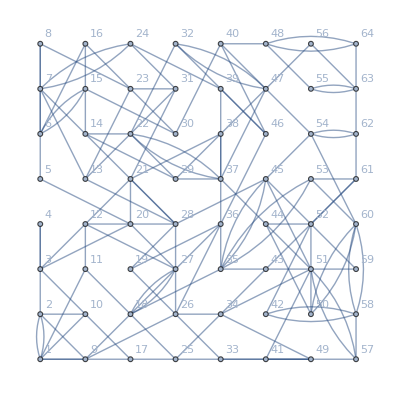
```mathematica
g=-Graphics-;
basisVectors={{0.33960707096610004,0.15636687718763573},{0.3852602208023346,0.19181414444301442},{0.40374020244896325,0.2284621485069517},{0.3991813832615329,0.21859773601871924},{0.3430155925749598,0.24372105447647444},{0.2512151052888425,0.18247415486359395},{0.2779576540482639,0.22934034107191456},{0.31109791832493905,0.24642746105738722},{0.47142841802607044,0.22826995237454814},{0.3671148175201015,0.18255010035906105},{0.4064379175506434,0.14919511144145922},{0.4241956048319075,0.19643196835345142},{0.3947242945287061,0.28807153374942257},{0.2756192121310822,0.262064784801146},{0.3627149950727307,0.2567487618780896},{0.32168516448593226,0.20980121743142668},{0.39803870862568214,0.16945277542025886},{0.25728663904598825,0.08359962245632482},{0.40184075965039534,0.17614487171938686},{0.39871118782988746,0.24118258879356255},{0.4096671868069825,0.26769631470779376},{0.26754247274314374,0.4412535047239809},{0.39475865236594254,0.3105487081491807},{0.33392656345812843,0.31883803325958426},{0.4461487335821549,0.07786730969581816},{0.33716439004486903,0.14823380594149885},{0.4290594262168753,0.20793165839555847},{0.4277271274564356,0.21524995613586426},{0.30841068019415097,0.4128769659095539},{0.34176304982445527,0.1732615564651248},{0.469091400972414,0.3802279505532591},{0.1272858954124699,0.5775111644568286},{0.44140650919021535,0.10661012147871668},{0.4502777624373041,0.09107458365350188},{0.33343814764932117,0.02594802988594403},{0.3270262990327673,0.1896553584561067},{0.34141502057516576,0.6748306445637567},{0.3397036720554441,0.2564397504618594},{0.3013372014918037,0.4195243212537757},{0.33152664664293474,0.03631551099838623},{0.49202651518493945,-0.005708226289110461},{0.4873767997579635,-0.9082843689694668},{0.4764972063418981,-0.010379671137295397},{0.49700400532218786,-0.513892994864353},{0.40435171088446953,0.0029534286493799453},{0.2193076771703487,0.24798510685051386},{0.01293108846461897,1.6038868671653477},{0.21189358552325435,0.02645757656693511},{0.4643577100280757,0.06963188597686026},{0.47354975284827233,-0.5145740814690549},{0.5399488439671989,0.03843887995467471},{0.5110959145243353,-0.5301310873471233},{0.5325165359355895,-0.29076706676648656},{0.5437799307819128,-0.3193613749765017},{0.16029542376667497,0.015746731159365816},{0.3043481789161073,0.13861118368651107},{0.5130306542824997,-0.2544329716541661},{0.4708360707388936,-1.1058205993243748},{0.23841572453085913,0.014577871922881703},{0.876736748274798,-1.0311914227522159},{0.5770907568971496,-0.2006920831730905},{0.5484611024177968,-0.3109017854327656},{0.2596303425050024,0.003863437823690071},{0.34638992841163957,0.03684888502251644}};
```

```mathematica
meloV=VectorPartition[basisVectors, V[g]/2,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g]/2, Method->MeloProbe,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];
```

{47,37,31,9,23,29,39,13,21,22,28,27,20,24,32,3,12,4,51,15,38,19,2,5,17,33,11,34,49,10,25,8,16,41,14,30,36,43,1,7,26,61,46,56,45,6,64,40,35,18,57,53,62,54,63,59,48,55,52,44,50,60,42,58}

g-Graphics-

basis:{{0.339607,0.156367},{0.38526,0.191814},{0.40374,0.228462},{0.399181,0.218598},{0.343016,0.243721},{0.251215,0.182474},{0.277958,0.22934},{0.311098,0.246427},{0.471428,0.22827},{0.367115,0.18255},{0.406438,0.149195},{0.424196,0.196432},{0.394724,0.288072},{0.275619,0.262065},{0.362715,0.256749},{0.321685,0.209801},{0.398039,0.169453},{0.257287,0.0835996},{0.401841,0.176145},{0.398711,0.241183},{0.409667,0.267696},{0.267542,0.441254},{0.394759,0.310549},{0.333927,0.318838},{0.446149,0.0778673},{0.337164,0.148234},{0.429059,0.207932},{0.427727,0.21525},{0.308411,0.412877},{0.341763,0.173262},{0.469091,0.380228},{0.127286,0.577511},{0.441407,0.10661},{0.450278,0.0910746},{0.333438,0.025948},{0.327026,0.189655},{0.341415,0.674831},{0.339704,0.25644},{0.301337,0.419524},{0.331527,0.0363155},{0.492027,-0.00570823},{0.487377,-0.908284},{0.476497,-0.0103797},{0.497004,-0.513893},{0.404352,0.00295343},{0.219308,0.247985},{0.0129311,1.60389},{0.211894,0.0264576},{0.464358,0.0696319},{0.47355,-0.514574},{0.539949,0.0384389},{0.511096,-0.530131},{0.532517,-0.290767},{0.54378,-0.319361},{0.160295,0.0157467},{0.304348,0.138611},{0.513031,-0.254433},{0.470836,-1.10582},{0.238416,0.0145779},{0.876737,-1.03119},{0.577091,-0.200692},{0.548461,-0.310902},{0.25963,0.00386344},{0.34639,0.0368489}}

meloN:15.2759

meloObj:164.

meloProbeN:15.2759

meloProbeObj:164.

Set::write: Tag Times in Null {{1,2},{1,2},{2,4},{2,18},{3,21},{3,4},{4,19},{4,12},{5,23},{5,14},{6,21},{6,12},{7,16},{7,6},{8,15},{8,23},{9,19},{9,1},{10,12},{10,12},{11,2},{11,25},«7»,{15,30},{16,6},{16,22},{17,3},{17,11},{18,17},{18,35},{19,25},{19,27},{20,11},{20,27},{21,4},{21,38},{22,38},{22,8},{23,22},{23,31},{24,32},{24,6},{25,11},{25,43},«78»} is Protected.

{58,42,63,1,60,57,52,29,51,41,59,2,6,53,10,54,25,12,7,49,34,43,22,33,39,16,45,21,23,44,31,56,8,48,3,26,27,47,40,4,37,38,18,64,46,50,17,55,30,20,15,36,32,62,11,13,14,28,35,24,5,19,61,9}

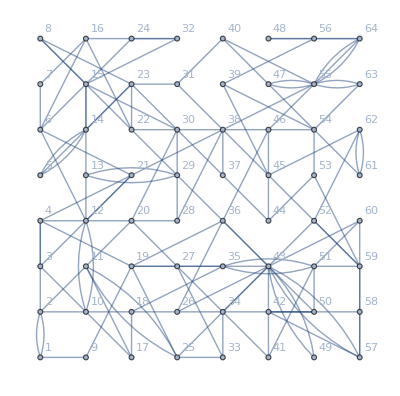
g-Graphics-

basis:{{0.165835,-1.97038},{0.263101,-0.930002},{0.368011,-0.163115},{0.36066,-0.179955},{0.254328,0.0150031},{0.451053,-0.0398453},{0.441362,-0.021603},{0.412277,0.015737},{0.0175747,1.93912},{0.438749,-0.0606255},{0.282106,-0.244235},{0.434705,-0.0644807},{0.331288,-0.00748126},{0.326619,0.0161675},{0.361455,0.00582227},{0.423582,-0.0110712},{0.330396,-0.230804},{0.332982,-0.292773},{0.324507,0.336408},{0.362366,-0.048933},{0.40489,-0.086296},{0.439012,0.0125472},{0.428277,0.0211313},{0.271319,-0.0117429},{0.446581,-0.0191445},{0.42713,0.10816},{0.422715,0.0896536},{0.304728,-0.0121234},{0.520904,0.0210231},{0.374188,0.0000715397},{0.428529,0.0433836},{0.354815,-0.00309381},{0.43648,0.00999852},{0.432056,-0.0482239},{0.298285,0.0302286},{0.393136,0.150836},{0.406026,0.0267502},{0.401932,0.00820525},{0.445419,0.0604117},{0.412283,0.0503739},{0.529098,0.08531},{0.62893,0.0889972},{0.453035,0.0577742},{0.43387,0.0642634},{0.436939,0.0509352},{0.414866,0.0972878},{0.41389,0.0517511},{0.423157,0.0734936},{0.457079,0.0616293},{0.397954,0.0537777},{0.527562,0.0695688},{0.552722,0.0283904},{0.472629,0.0610418},{0.462507,0.0523664},{0.386341,0.0482768},{0.428722,0.0702231},{0.569171,0.0762796},{0.789346,0.110357},{0.513422,0.0587852},{0.592677,0.0818033},{0.205724,0.0233817},{0.352299,0.0334498},{0.621639,0.0783152},{0.409503,0.0690537}}

meloN:14.9682

meloObj:148.

meloProbeN:15.2003

meloProbeObj:180.

```mathematica
For[i=1,i≤1,i+=1,
(*Module[{g,grounds,basisVectors,meloV, meloProbeV,meloN,meloObj,meloProbeN,meloProbeObj},*)
g =RandomGrid1[8,8,maxDist=2,maxFanOut=2];
(* EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]];*)
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g;
{grounds,basisVectors} = FingerprintVectors[g,2, GroundingRandom];
basisVectors = Re[basisVectors];
meloV=VectorPartition[basisVectors, V[g]/2,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g]/2, Method->MeloProbe,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];](*]*)
```

```mathematica
meloV=VectorPartition[basisVectors, V[g]/2,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]]
meloProbeV=VectorPartition[basisVectors, V[g]/2, Method->MeloProbe,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]]
```

148.

{58,42,63,1,60,57,52,29,51,41,59,2,6,53,10,54,25,12,7,49,34,43,22,33,39,16,45,21,23,44,31,56,8,48,3,26,27,47,40,4,37,38,18,64,46,50,17,55,30,20,15,36,32,62,11,13,14,28,35,24,5,19,61,9}

180.

```mathematica
g=-Graphics-;
basisVectors={{0.16583476167236771,-1.9703781701703487},{0.2631011760433074,-0.9300016176534769},{0.368011410256321,-0.16311484533989476},{0.36066038737032774,-0.17995497845927716},{0.25432791939509014,0.015003053200389993},{0.45105273673162394,-0.039845286005129904},{0.4413615859973928,-0.021603039230415923},{0.41227729822578846,0.015737030522888436},{0.01757467579043465,1.9391187773568561},{0.43874881338403415,-0.060625548214992},{0.2821063057356382,-0.24423453030208098},{0.43470474314034807,-0.0644807281543974},{0.3312879202092956,-0.0074812603891672375},{0.3266189136899025,0.016167507888631003},{0.3614549714740616,0.005822273441207009},{0.4235822947757894,-0.011071152334510278},{0.33039579325259827,-0.23080387160243382},{0.3329815232784635,-0.29277259904413794},{0.3245065572656256,0.336407984809347},{0.3623657289776246,-0.0489330110149278},{0.40488990965866484,-0.08629604583678067},{0.43901207870793557,0.012547166414921856},{0.42827670400799595,0.021131291833727167},{0.27131850479927644,-0.011742912174181035},{0.44658068991728866,-0.01914451111837305},{0.4271298533345025,0.10816027472660698},{0.42271479313074733,0.0896535976773829},{0.3047282403785419,-0.012123394919626268},{0.5209038257354011,0.02102305327770562},{0.37418794757911616,0.0000715397010994159},{0.42852901227286777,0.04338358550699548},{0.3548146371788332,-0.003093810396224015},{0.4364800328525768,0.009998517124785713},{0.43205647502232214,-0.04822389506345613},{0.298284508308254,0.03022862826400322},{0.39313614858932927,0.15083603525667594},{0.4060259525699849,0.026750179286306186},{0.4019321303073312,0.00820524889598451},{0.4454191249437846,0.06041169413801269},{0.41228273778530994,0.050373934173333294},{0.5290980884782344,0.08530998327116995},{0.6289295196150291,0.08899722484532316},{0.4530354175923037,0.05777415431772471},{0.43386963933613537,0.06426338938302675},{0.4369394545379255,0.05093517063511023},{0.4148656240866952,0.09728782314607473},{0.4138900797819719,0.05175107594772101},{0.42315669245645327,0.07349357466642252},{0.4570794878359898,0.06162933425712914},{0.3979544191831215,0.05377769846586814},{0.5275618122015547,0.06956876741199046},{0.5527217842877546,0.02839044332085559},{0.47262920086435417,0.06104180583788543},{0.4625074792277699,0.052366447365799595},{0.38634098081371776,0.04827678118647361},{0.4287223005782861,0.07022310453432043},{0.5691713253299645,0.07627955734545992},{0.7893457878210278,0.11035667248170716},{0.5134223435417852,0.0587852208860211},{0.5926770527007528,0.08180331803007769},{0.20572370415525862,0.0233816573438006},{0.35229919690589234,0.03344982213059397},{0.6216387906712888,0.07831518480877882},{0.40950294384724845,0.06905368491971428}};
```

```mathematica
meloV=VectorPartition[basisVectors, V[g]/2,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g]/2, Method->MeloProbe,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];
```

g-Graphics-

basis:{{0.165835,-1.97038},{0.263101,-0.930002},{0.368011,-0.163115},{0.36066,-0.179955},{0.254328,0.0150031},{0.451053,-0.0398453},{0.441362,-0.021603},{0.412277,0.015737},{0.0175747,1.93912},{0.438749,-0.0606255},{0.282106,-0.244235},{0.434705,-0.0644807},{0.331288,-0.00748126},{0.326619,0.0161675},{0.361455,0.00582227},{0.423582,-0.0110712},{0.330396,-0.230804},{0.332982,-0.292773},{0.324507,0.336408},{0.362366,-0.048933},{0.40489,-0.086296},{0.439012,0.0125472},{0.428277,0.0211313},{0.271319,-0.0117429},{0.446581,-0.0191445},{0.42713,0.10816},{0.422715,0.0896536},{0.304728,-0.0121234},{0.520904,0.0210231},{0.374188,0.0000715397},{0.428529,0.0433836},{0.354815,-0.00309381},{0.43648,0.00999852},{0.432056,-0.0482239},{0.298285,0.0302286},{0.393136,0.150836},{0.406026,0.0267502},{0.401932,0.00820525},{0.445419,0.0604117},{0.412283,0.0503739},{0.529098,0.08531},{0.62893,0.0889972},{0.453035,0.0577742},{0.43387,0.0642634},{0.436939,0.0509352},{0.414866,0.0972878},{0.41389,0.0517511},{0.423157,0.0734936},{0.457079,0.0616293},{0.397954,0.0537777},{0.527562,0.0695688},{0.552722,0.0283904},{0.472629,0.0610418},{0.462507,0.0523664},{0.386341,0.0482768},{0.428722,0.0702231},{0.569171,0.0762796},{0.789346,0.110357},{0.513422,0.0587852},{0.592677,0.0818033},{0.205724,0.0233817},{0.352299,0.0334498},{0.621639,0.0783152},{0.409503,0.0690537}}

meloN:14.9682

meloObj:148.

meloProbeN:15.2003

meloProbeObj:180.

```mathematica
(**)
ds=Table[
With[{iv=VectorMaxOnDirection[basisVectors,V[g]/2,{Cos[2*Pi/40*i],Sin[2*Pi/200*i]}, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]},
Total[basisVectors*iv]]
,{i,200}];
```

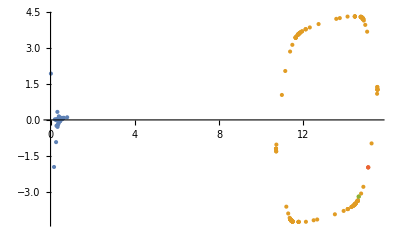

```mathematica
ListPlot[{basisVectors,ds,{Total[basisVectors*meloV]}, {Total[basisVectors*meloProbeV]}}]
(*ListPlot[basisVectors]
ListPlot[{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}]*)
```

```mathematica
g
```

-Graphics-

```mathematica
grounds
```

{9,1}

```mathematica
g=-Graphics-;
basisVectors={{0.16583476167236771,-1.9703781701703487},{0.2631011760433074,-0.9300016176534769},{0.368011410256321,-0.16311484533989476},{0.36066038737032774,-0.17995497845927716},{0.25432791939509014,0.015003053200389993},{0.45105273673162394,-0.039845286005129904},{0.4413615859973928,-0.021603039230415923},{0.41227729822578846,0.015737030522888436},{0.01757467579043465,1.9391187773568561},{0.43874881338403415,-0.060625548214992},{0.2821063057356382,-0.24423453030208098},{0.43470474314034807,-0.0644807281543974},{0.3312879202092956,-0.0074812603891672375},{0.3266189136899025,0.016167507888631003},{0.3614549714740616,0.005822273441207009},{0.4235822947757894,-0.011071152334510278},{0.33039579325259827,-0.23080387160243382},{0.3329815232784635,-0.29277259904413794},{0.3245065572656256,0.336407984809347},{0.3623657289776246,-0.0489330110149278},{0.40488990965866484,-0.08629604583678067},{0.43901207870793557,0.012547166414921856},{0.42827670400799595,0.021131291833727167},{0.27131850479927644,-0.011742912174181035},{0.44658068991728866,-0.01914451111837305},{0.4271298533345025,0.10816027472660698},{0.42271479313074733,0.0896535976773829},{0.3047282403785419,-0.012123394919626268},{0.5209038257354011,0.02102305327770562},{0.37418794757911616,0.0000715397010994159},{0.42852901227286777,0.04338358550699548},{0.3548146371788332,-0.003093810396224015},{0.4364800328525768,0.009998517124785713},{0.43205647502232214,-0.04822389506345613},{0.298284508308254,0.03022862826400322},{0.39313614858932927,0.15083603525667594},{0.4060259525699849,0.026750179286306186},{0.4019321303073312,0.00820524889598451},{0.4454191249437846,0.06041169413801269},{0.41228273778530994,0.050373934173333294},{0.5290980884782344,0.08530998327116995},{0.6289295196150291,0.08899722484532316},{0.4530354175923037,0.05777415431772471},{0.43386963933613537,0.06426338938302675},{0.4369394545379255,0.05093517063511023},{0.4148656240866952,0.09728782314607473},{0.4138900797819719,0.05175107594772101},{0.42315669245645327,0.07349357466642252},{0.4570794878359898,0.06162933425712914},{0.3979544191831215,0.05377769846586814},{0.5275618122015547,0.06956876741199046},{0.5527217842877546,0.02839044332085559},{0.47262920086435417,0.06104180583788543},{0.4625074792277699,0.052366447365799595},{0.38634098081371776,0.04827678118647361},{0.4287223005782861,0.07022310453432043},{0.5691713253299645,0.07627955734545992},{0.7893457878210278,0.11035667248170716},{0.5134223435417852,0.0587852208860211},{0.5926770527007528,0.08180331803007769},{0.20572370415525862,0.0233816573438006},{0.35229919690589234,0.03344982213059397},{0.6216387906712888,0.07831518480877882},{0.40950294384724845,0.06905368491971428}};
```

```mathematica
meloV=VectorPartition[basisVectors, V[g]/2,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g]/2, Method->MeloProbe,OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];
```

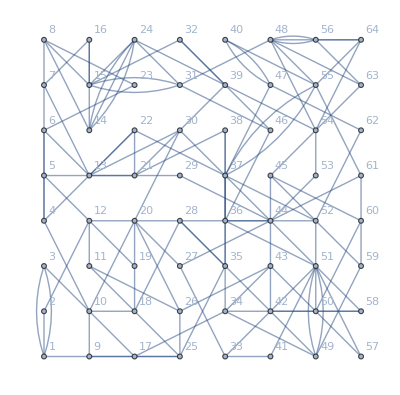
```mathematica
g=-Graphics-;
basisVectors={{0.24908291746546912,-0.022783530194473288},{0.30379291271921516,-0.04759413997557452},{0.32174557109865987,0.0023369521553353507},{0.34392381171443975,-1.45389505174135},{0.35366828107560566,-0.6154029949803242},{0.35172251356879736,-0.6338854391982628},{0.387994315058084,-0.26422640502416883},{0.4239065356680357,-0.4453648280638064},{0.35725791209844904,-0.05068631328755335},{0.3290786591785075,-0.28921978834459516},{0.36476105136859605,0.05383637679893112},{0.3449676340274086,-0.07721413008657511},{0.3605238910462244,-0.3014267392250086},{0.38646833983757906,-0.23157129452013803},{0.41779046653195734,-0.204518034245278},{0.40192946512439104,-0.23183545115322862},{0.4535356044194887,0.047768536525053994},{0.34389819471737787,-0.022043226873501204},{0.3200335156428499,0.09016269385464934},{0.25769944423821073,0.3649360581941246},{0.41386654100140646,-0.2563183489644004},{0.3748107830058342,-0.5112803074883401},{0.26305477439412855,-0.3581469623107231},{0.5464852122249578,-0.2427327868567766},{0.3837991933847782,0.05668014853390261},{0.35198105274804886,0.1772337316195663},{0.021562302413630306,1.7254326168952334},{0.3690471353852237,0.1281180335395432},{0.37576311240582505,0.05005528413467261},{0.2523064172624652,0.11626165661586772},{0.6371760870767773,-0.1710257585522583},{0.4837102251520288,-0.14095876117549355},{0.2351223978360783,0.9470237688269995},{0.41605889605185536,0.17559702621329576},{0.377925072343756,0.05043903068361507},{0.41143557658807767,0.0823191653320419},{0.3673936143157135,-0.03829047035249942},{0.4020770019502501,-0.06916009121831922},{0.5045192140577647,-0.14821563825583173},{0.22849963447811145,0.018822960936961283},{0.3063090963102277,0.6875541528042538},{0.3874424420721507,0.28787118647982124},{0.38812924805505794,0.22867296262140646},{0.3774670598198731,0.39672792716445426},{0.48643265726492413,0.2585591239305412},{0.5152857209208118,-0.07495199135526938},{0.29709914569799833,0.012253575136583452},{0.6378172081518726,0.03780843216366781},{0.3952819416531161,0.31755870256837765},{0.41837683559798317,0.1968563836897039},{0.36396052083882446,0.4232751564516088},{0.3903024315054578,0.0726359819235389},{0.4757409688362693,0.22193763556889864},{0.5604796039071132,0.04233796364344454},{0.3748644837907835,0.03940592734440066},{0.8545264327526529,0.08768647558715571},{0.3828125214197175,0.3283787497014572},{0.3944383574848369,0.304270702317011},{0.43145205451837343,0.2729656069156508},{0.45917238340422983,0.23011244397507266},{0.3991062906915275,0.23796961391813565},{0.35046842557450447,0.04484946869501003},{0.6641038573716673,0.1296211373370888},{0.6103057506369938,0.053012044767142066}};
```

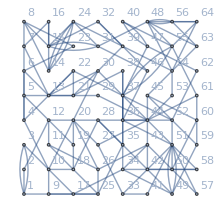
g-Graphics-

basis:{{0.249083,-0.0227835},{0.303793,-0.0475941},{0.321746,0.00233695},{0.343924,-1.4539},{0.353668,-0.615403},{0.351723,-0.633885},{0.387994,-0.264226},{0.423907,-0.445365},{0.357258,-0.0506863},{0.329079,-0.28922},{0.364761,0.0538364},{0.344968,-0.0772141},{0.360524,-0.301427},{0.386468,-0.231571},{0.41779,-0.204518},{0.401929,-0.231835},{0.453536,0.0477685},{0.343898,-0.0220432},{0.320034,0.0901627},{0.257699,0.364936},{0.413867,-0.256318},{0.374811,-0.51128},{0.263055,-0.358147},{0.546485,-0.242733},{0.383799,0.0566801},{0.351981,0.177234},{0.0215623,1.72543},{0.369047,0.128118},{0.375763,0.0500553},{0.252306,0.116262},{0.637176,-0.171026},{0.48371,-0.140959},{0.235122,0.947024},{0.416059,0.175597},{0.377925,0.050439},{0.411436,0.0823192},{0.367394,-0.0382905},{0.402077,-0.0691601},{0.504519,-0.148216},{0.2285,0.018823},{0.306309,0.687554},{0.387442,0.287871},{0.388129,0.228673},{0.377467,0.396728},{0.486433,0.258559},{0.515286,-0.074952},{0.297099,0.0122536},{0.637817,0.0378084},{0.395282,0.317559},{0.418377,0.196856},{0.363961,0.423275},{0.390302,0.072636},{0.475741,0.221938},{0.56048,0.042338},{0.374864,0.0394059},{0.854526,0.0876865},{0.382813,0.328379},{0.394438,0.304271},{0.431452,0.272966},{0.459172,0.230112},{0.399106,0.23797},{0.350468,0.0448495},{0.664104,0.129621},{0.610306,0.053012}}

meloN:12.2907

meloObj:66.4935

meloProbeN:12.2907

meloProbeObj:66.4935

```mathematica
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];
```

```mathematica
(**)
ds=Table[
With[{iv=VectorMaxOnDirection[basisVectors,V[g]/2,{Cos[2*Pi/40*i],Sin[2*Pi/200*i]}, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]},
Total[basisVectors*iv]]
,{i,200}];
```

```mathematica
ListPlot[{basisVectors,ds,{Total[basisVectors*meloV]}, {Total[basisVectors*meloProbeV]}}]
(*ListPlot[basisVectors]
ListPlot[{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}]*)
```

-Graphics-

```mathematica
g
```

-Graphics-

```mathematica
grounds
```

{9,1}